#### Cox’s Proportional Hazard Model

```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
β10=1;
β20=5;
λ0=1;
Dim=3;
h0[λ_,t_]=Simplify[PDF[ExponentialDistribution[λ],t]/(1-CDF[ExponentialDistribution[λ],t]),t>0];
```

```mathematica
u[a,β1,β2,x1,x2,t,d]//Simplify
```

u[a,β1,β2,x1,x2,t,d]

```mathematica
h[λ_,β1_,β2_,x1_,x2_,t_]=h0[λ,t]Exp[x1 β1+x2 β2];
F[λ_,β1_,β2_,x1_,x2_,t_]=1-Exp[-h[λ,β1,β2,x1,x2,t] t];
f[λ_,β1_,β2_,x1_,x2_,t_,d_]=(D[F[λ,β1,β2,x1,x2,t],t])^d(1-F[λ,β1,β2,x1,x2,t])^(1-d);
u[λ_,β1_,β2_,x1_,x2_,t_,d_]=-PowerExpand[Log[f[λ,β1,β2,x1,x2,t,d]]];
U[x1_,x2_,t_]=u[λ0,β10,β20,x1,x2,t,1]
dU[x_,y_,z_]=GradientG[U[x,y,z],{x,y,z}];
ddU[x_,y_,z_]=HessianH[U[x,y,z],{x,y,z}]+IdentityMatrix[Dim];
INTERVAL=1001;
STEPS=5;
CHAINS=5;
dt10=0.0000000001;
dt20=0.0000000001;

qinit=RandomVariate[UniformDistribution[],{CHAINS,Dim}];
outbnd[q_]:=q[[3]]≤0(*||AnyTrue[q[[1;;2]],(Abs[#]>1)&]*);
```

ⅇ^(x1+5 x2) t-x1-5 x2

```mathematica
QS=hmc[U,dU,ddU,3,5000,10000,True,True,qinit];
```

10018337.4713.27040.3558410.374529-18.7848318.685.16362×10^60.0002153180.00144855True{1,3}{1,6}

LinearSolve::krymit: The maximum number of iterations, 30, has been reached by the Krylov algorithm without convergence to a solution within the required tolerance. The currently computed solution has been returned.

20023050.652.629350.2412830.428021-18.19139.04493032.460.002822820.0655605False{1,4,6}{1,2,6}

30031.122237.910060.7635740.433432-0.4072040.71502348.44060.02527640.170047True{1,2}{3,6}

400452.46942.815620.3239210.443818-6.115-5.7411146.35440.04477870.140535False{2,3,4,6}{1}

General::munfl: Exp[-802.784] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^802.784 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

5005-15.80236.197750.5966150.4204898.68708-7.1151822.480.06556050.248966True{1,2,4,6}{1,3,6}

600619.07340.15960.2442990.43323.4066-7.1151822.480.06556050.248966False{1,2,4,6}{1,3,6}

7007-11.91046.975320.3223650.4100194.79518-7.1151822.480.06556050.248966True{1,2,4,6}{1,3,6}

80089.162674.757760.8908070.17860613.3173-7.1151822.480.06556050.248966False{1,2,4,6}{1,3,6}

9009-8.426398.37650.6335740.3677371.31121-7.1151822.480.06556050.248966True{1,2,4,6}{1,3,6}

```mathematica
ListPointPlot3D[QS,AxesLabel->{Subscript[x, 1],Subscript[x, 2],t}]
```

-Graphics3D-

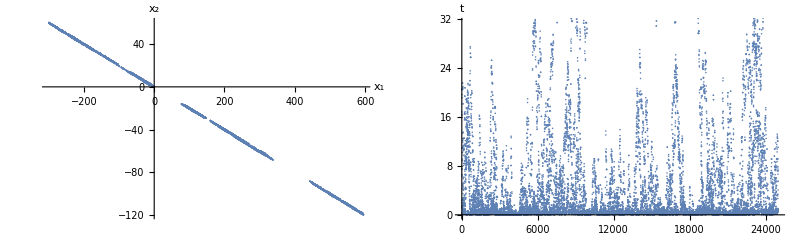

```mathematica
GraphicsRow[{ListPlot[QS[[;;,1;;2]],AxesLabel->{Subscript[x, 1],Subscript[x, 2]}],ListPlot[QS[[;;,3]],AxesLabel->t]}]
```

```mathematica
n=20;
mQS=RandomChoice[QS,n];
dd=Table[1,n];For[i=1,i≤n,i++,If[mQS[[i,3]]>1/λ0,mQS[[i,3]]=1/λ0;dd[[i]]=0]];

Dim=3;
U1[λ_,β1_,β2_]=Sum[u[λ,β1,β2,mQS[[i,1]],mQS[[i,2]],mQS[[i,3]],dd[[i]]],{i,1,Length[mQS]}];
dU1[a_,y_,z_]=GradientG[U1[a,y,z],{a,y,z}];
ddU1[a_,y_,z_]=HessianH[U1[a,y,z],{a,y,z}]+IdentityMatrix[Dim];
INTERVAL=1001;
STEPS=5;
CHAINS=5;
dt10=0.00000000001;
dt20=0.00000000001;
switch0=1;
(*qinit=RandomVariate[UniformDistribution[],{CHAINS,Dim}];*)
(*qinit=Table[{a0,b0,β10,β20},CHAINS];*)
mle=FindMinimum[{U1[a,c,d],a>0&&c>0&&d>0},{{a,.1},{c,.1},{d,.1}}];
qinit=Table[{a,c,d}/.Last[mle],CHAINS];
(*qinit=Table[{1,.5,1},CHAINS];*)
outbnd[q_]:=q[[1]]<0||AnyTrue[q[[2;;3]],(Abs[#]>100)&];
(*outbnd[q_]=False;*)
QS2=hmc[U1,dU1,ddU1,Dim,5000,10000,True,True,qinit];
```

10012.71766×10^133.916790.392360.398373-42.09611.97209×10^92.71766×10^132.72642×10^-82.01762×10^-7False{1,2}{6}

20022.70556×10^75.698840.4694010.502603-39.76532.70555×10^76.50587×10^122.68545×10^-73.93177×10^-7True{1,2,6}{1,6}

30031.17014×10^122.161890.2947430.335307-38.47971.40952×10^61.17014×10^121.35735×10^-61.23396×10^-6False{1,3}{6}

40049926.7111.50980.1952190.431655-43.40099883.314.96253×10^110.00002153181.80664×10^-6True{1,4}{1,6}

50051.43747×10^111.075950.4581930.39055-39.0257347.1481.43747×10^110.00008176713.87269×10^-6False{1,3}{6}

6006388.5779.201170.4367410.519622-41.4285347.1481.43747×10^110.00008176713.87269×10^-6True{1,3}{6}

70071.43747×10^114.273860.2719480.206191-39.8572347.1481.43747×10^110.00008176713.87269×10^-6False{1,3}{6}

LinearSolve::krymit: The maximum number of iterations, 30, has been reached by the Krylov algorithm without convergence to a solution within the required tolerance. The currently computed solution has been returned.

8008383.0676.23190.4155420.534114-35.9192347.1481.43747×10^110.00008176713.87269×10^-6True{1,3}{6}

90091.43747×10^110.831980.2611360.324993-46.0669347.1481.43747×10^110.00008176713.87269×10^-6False{1,3}{6}

```mathematica
Export["mQS.csv",mQS];
Export["dd.csv",dd];
```

```mathematica
Median[QS2]
```

{1.33333,1.04867,5.24386}

```mathematica
StandardDeviation[QS2]
```

{0.987077,0.394787,1.97074}

```mathematica
QS2//Dimensions
```

{25000,3}

```mathematica
ListPointPlot3D[QS2,AxesLabel->{λ,Subscript[β, 1],Subscript[β, 2]}]
```

-Graphics3D-

```mathematica
psrf[QS2]
```

{1.00401,1.0015,1.0015}

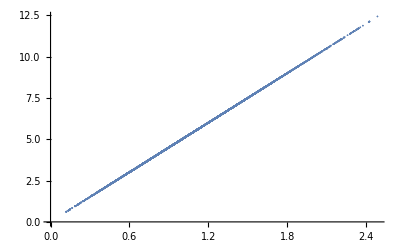

```mathematica
ListPlot[QS2[[;;,2;;3]]]
```

```mathematica
Covariance[QS2]//MatrixForm
```

(0.974321 | -0.316295 | -1.57736
-0.316295 | 0.155857 | 0.778021
-1.57736 | 0.778021 | 3.88383)

```mathematica
m=Mean[QS2]
```

{1.55514,1.08081,5.40648}

```mathematica
qt=Quantile[QS2,{.025,.975}]
```

{{0.31769,4.02797},{0.401183,1.91848},{2.00701,9.58617}}

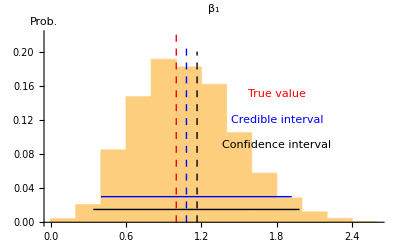

```mathematica
Show[Histogram[QS2[[;;,2]],Automatic,"Probability",AxesLabel->"Prob.",PlotLabel->Subscript[β, 1]],
Graphics[{Thick,Black,Line[{{0.34,.015},{1.98,.015}}]}],
Graphics[{Thick,Blue,Line[{{qt[[2,1]],.03},{qt[[2,2]],.03}}]}],Graphics[{Red,Text["True value",{1.8,.15}]}],
Graphics[{Blue,Text["Credible interval",{1.8,.12}]}],
Graphics[{Black,Text["Confidence interval",{1.8,.09}]}],Graphics[{Red,Thick,Dashed,Line[{{β10,.0},{β10,.22}}]}],Graphics[{Blue,Thick,Dashed,Line[{{m[[2]],.0},{m[[2]],.21}}]}],Graphics[{Black,Thick,Dashed,Line[{{1.1654,.0},{1.1654,.20}}]}]]
```

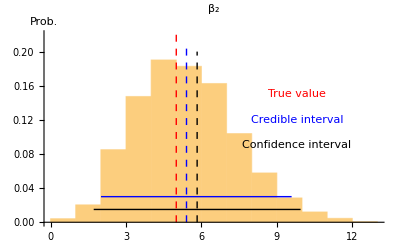

```mathematica
Show[Histogram[QS2[[;;,3]],Automatic,"Probability",AxesLabel->"Prob.",PlotLabel->Subscript[β, 2]],
Graphics[{Thick,Black,Line[{{1.716732,.015},{9.942068,.015}}]}],
Graphics[{Thick,Blue,Line[{{qt[[3,1]],.03},{qt[[3,2]],.03}}]}],Graphics[{Red,Text["True value",{9.8,.15}]}],
Graphics[{Blue,Text["Credible interval",{9.8,.12}]}],
Graphics[{Black,Text["Confidence interval",{9.8,.09}]}],Graphics[{Red,Thick,Dashed,Line[{{β20,.0},{β20,.22}}]}],Graphics[{Blue,Thick,Dashed,Line[{{m[[3]],.0},{m[[3]],.21}}]}],Graphics[{Black,Thick,Dashed,Line[{{5.8294,.0},{5.8294,.20}}]}]]
```

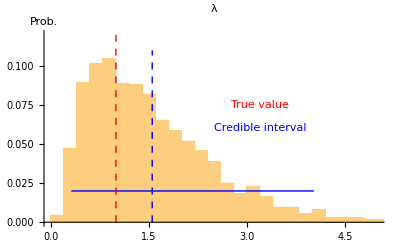

```mathematica
Show[Histogram[QS2[[;;,1]],Automatic,"Probability",AxesLabel->"Prob.",PlotLabel->λ],
Graphics[{Thick,Blue,Line[{{qt[[1,1]],.02},{qt[[1,2]],.02}}]}],Graphics[{Red,Text["True value",{3.2,.075}]}],
Graphics[{Blue,Text["Credible interval",{3.2,.06}]}],
Graphics[{Red,Thick,Dashed,Line[{{β10,.0},{β10,.12}}]}],Graphics[{Blue,Thick,Dashed,Line[{{m[[1]],.0},{m[[1]],.11}}]}]]
```

```mathematica
Join[{Mean[QS2],StandardDeviation[QS2]}//Transpose,Quantile[QS2,{.025,.975}]]//Transpose//MatrixForm
```

(1.55514 | 1.08081 | 5.40648 | 0.31769 | 0.401183 | 2.00701
0.987077 | 0.394787 | 1.97074 | 4.02797 | 1.91848 | 9.58617)

```mathematica
S[λ_,β1_,β2_,x1_,x2_,t_]=1-F[λ,β1,β2,x1,x2,t]
```

ⅇ^(-ⅇ^(x1 β1+x2 β2) t λ)

```mathematica
x10
```

129.513

```mathematica
x20
```

-25.8144

```mathematica
x10=Median[QS][[1]];
x20=Median[QS][[2]];
```

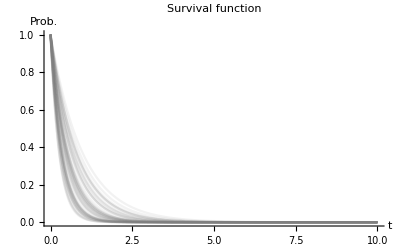

```mathematica
t1=Table[S[QS2[[i 100,1]],QS2[[i 100,2]],QS2[[i 100,3]],x10,x20,t],{i,1,50}];Plot[t1,{t,0.,10},PlotStyle->Directive[Opacity[0.1],Gray],PlotRange->All,PlotLabel->"Survival function",AxesLabel->{"t","Prob."}]
```

```mathematica
Median[ExponentialDistribution[1]]//N
```

0.693147

```mathematica
sol=Solve[S[a,b,c,x10,x20,t]==0.5,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(0.693147 ⅇ^(-129.513 b+25.8144 c))/a}}

```mathematica
t2=sol[[1]][[1]][[2]]/.{a->QS2[[;;,1]],b->QS2[[;;,2]],c->QS2[[;;,3]]};
```

```mathematica
Mean[t2]
```

0.396489

```mathematica
Quantile[t2,{.025,.975}]
```

{0.591355,2.96722}

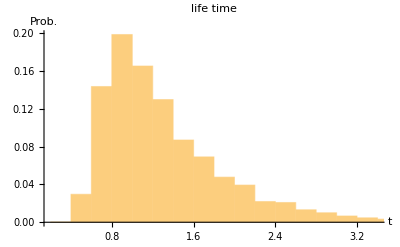

```mathematica
Histogram[t2,Automatic,"Probability",AxesLabel->{"t","Prob."},PlotLabel->"life time"]
```

```mathematica
Mean[QS2]
```

{1.55514,1.08081,5.40648}